```mathematica
(* Answer to problem set/exam question FriedmanPIH *)
```

```mathematica
(* Setup and housekeeping stuff *)
ClearAll["Global`*"];
If[Length[$FrontEnd] > 0,NBDir=SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
rootDir = SetDirectory["../../.."];(* root directory below which all code resides *)
CoreCodeDir=SetDirectory[rootDir<>"/Mathematica/CoreCode"];
MainCodeDir=SetDirectory[rootDir<>"/Mathematica/Examples/Question"];
FigsDir=SetDirectory[MainCodeDir<>"/Figures"];
Get[CoreCodeDir<>"/FriedmanPIH-Setup.m"];(* Further setup stuff, for creating figures etc *)
```

```mathematica
(* Function to construct all results using variances as inputs *)
MakeResults[𝓅Var_,ϑVar_,ColorForPlots_] := Block[{𝓅Std,ϑStd,α1FriedmanTheory,α0Est,α1Est},
{𝓅Std,ϑStd}={𝓅Var^0.5,ϑVar^0.5}; (* Compute standard deviations from variances *)
(* Create normally distributed shocks according to the assumed distributions *)
ϑVec=RandomVariate[NormalDistribution[0,ϑStd],NObs];(* ϑVec is the list (vector) of transitory shocks *)
𝓅Vec=𝓅Mean+RandomVariate[NormalDistribution[0,𝓅Std],NObs];(* 𝓅Vec is the list (vector) of permanent incomes *)
(* 𝓅Mean is an "environment" variable *)
𝓎Vec=𝓅Vec+ϑVec; (* Actual income is permanent income plus transitory *)
𝒸Vec=𝓅Vec;(* Consumption equals permanent income! *)
FitLine=LinearModelFit[Transpose[{𝓎Vec,𝒸Vec}],{1,𝓎},𝓎];(* Regress 𝒸 on 𝓎 and a constant *)
{α0Est,α1Est}=FitLine["BestFitParameters"];
Print["Predicted coefficient from Friedman formula vs estimated from data:",{α1FriedmanTheory=𝓅Var/(𝓅Var+ϑVar),α1Est}];
FitPlot=Plot[FitLine[𝓎],{𝓎,Min[𝓎Vec],Max[𝓎Vec]},PlotStyle->ColorForPlots];
Degree45=Plot[𝓎,{𝓎,0,Max[𝓎Vec]},PlotStyle->Black];
FitComparedToCEqualsY=Show[Degree45,FitPlot];
DotPlot=ListPlot[Transpose[{𝓎Vec,𝒸Vec}],PlotStyle->ColorForPlots];
Return[{α1Est,α1FriedmanTheory,FitComparedToCEqualsY,DotPlot}]];
```

```mathematica
(* Set parameter values *)
𝓅VarBase=0.01; (* Standard deviation of permanent income 𝓅 *)
ϑVarBase=0.02;(* Standard deviation of transitory income ϑ *)
𝔊Base=1.0; (* Growth factor; useful for creating trending time series if 𝔊 > 1.0 *)
𝓅Mean=𝓅MeanBase = 1.0; (* Level of permanent income to start with *)
NObs=100; (* Number of observations to create *)
FarmerColor=Red;
BaseColor=NonFarmerColor=Blue;
```

```mathematica
AllResults={};(* List for accumulating results across experiments *)
```

Predicted coefficient from Friedman formula vs estimated from data:{0.333333,0.359995}

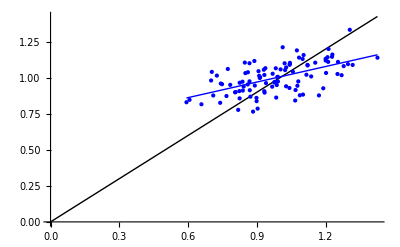

```mathematica
{α1Est,α1FriedmanTheory,FitPlotBase,DotPlotBase}=MakeResults[𝓅VarBase,ϑVarBase,NonFarmerColor];
AppendTo[AllResults,{α1Est,α1FriedmanTheory}];
{𝓎VecBase,𝒸VecBase}={𝓎Vec,𝒸Vec};
Print[Show[FitPlotBase,DotPlotBase]];
```

```mathematica
(* Example where farmers have larger transitory variance *)
ϑVarFarm1=3 ϑVarBase;
{α1Est,α1FriedmanTheory,FitPlotFarm1,DotPlotFarm1}=MakeResults[𝓅VarBase,ϑVarFarm1,FarmerColor];
AppendTo[AllResults,{α1Est,α1FriedmanTheory}];
```

Predicted coefficient from Friedman formula vs estimated from data:{0.142857,0.17033}

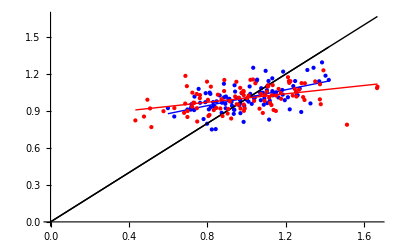

```mathematica
Print[Farm1Plot=Show[FitPlotBase,DotPlotBase,FitPlotFarm1,DotPlotFarm1,PlotRange->All]];
```

Predicted coefficient from Friedman formula vs estimated from data:{0.833333,0.853889}

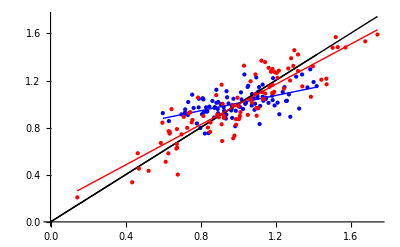

```mathematica
𝓅VarFarm2=10 𝓅VarBase;
{α1Est,α1FriedmanTheory,FitPlotFarm2,DotPlotFarm2}=MakeResults[𝓅VarFarm2,ϑVarBase,FarmerColor];
AppendTo[AllResults,{α1Est,α1FriedmanTheory}];
Print[Farm2Plot=Show[FitPlotBase,DotPlotBase,FitPlotFarm2,DotPlotFarm2,PlotRange->All]];
```

Predicted coefficient from Friedman formula vs estimated from data:{0.0163934,0.0126963}

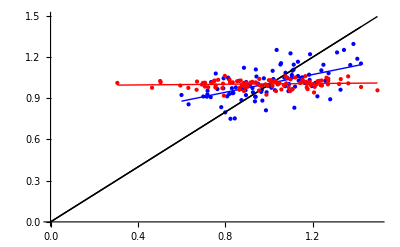

```mathematica
𝓅VarFarm3=0.10 𝓅VarBase;
ϑVarFarm3= 3 ϑVarBase;

{α1Est,α1FriedmanTheory,FitPlotFarm3,DotPlotFarm3}=MakeResults[𝓅VarFarm3,ϑVarFarm3,FarmerColor];
AppendTo[AllResults,{α1Est,α1FriedmanTheory}];
Print[Farm3Plot=Show[FitPlotBase,DotPlotBase,FitPlotFarm3,DotPlotFarm3,PlotRange->All]];
```

```mathematica
ExportFigure[Farm1Plot,"Farm1Plot"];
ExportFigure[Farm2Plot,"Farm2Plot"];
ExportFigure[Farm3Plot,"Farm3Plot"];
```

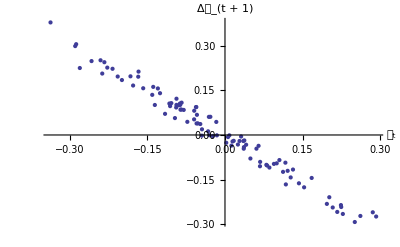

```mathematica
ϑVectp1=RandomVariate[NormalDistribution[0,ϑVarBase],NObs];(* Draw a different set of transitory shocks than the original one, and construct t+1 income *)
𝓎Vectp1=𝓅Vec+ϑVectp1; (* Period t+1 income is permanent income plus transitory in t+1 *)
Δ𝓎=𝓎Vectp1-𝓎Vec;
𝓈t=𝓎Vec-𝒸Vec;
stVsytPlot=ListPlot[Transpose[{𝓈t,Δ𝓎}]
,AxesLabel->{"𝓈_t","Δ𝓎_(t + 1)"}];
Print[ExportFigure[stVsytPlot,"stVsytPlot"]];
```